# Hermitian into unitary transformation

Transform a Hermitian operator into a unitary one

## Example Content

Utilizing the parameter-shift rule involves transforming the eigenvalues of a Hermitian operator into ±1, thereby converting it into a unitary operator. This technique is widely employed for measuring gradients of quantum circuits in relation to their parameters.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Generate a pseudorandom GUE matrix:

```mathematica
h=RandomVariate[GaussianUnitaryMatrixDistribution[2]]
```

{{0.257008+0. ⅈ,0.158164+0.26653 ⅈ},{0.158164-0.26653 ⅈ,1.35714+0. ⅈ}}

Check if it is unitary or Hermitian:

```mathematica
Through[{UnitaryMatrixQ,HermitianMatrixQ}[h]]
```

{False,True}

Calculate its eigenvalues:

```mathematica
{e0,e1}=Eigenvalues[h]
```

{1.43845,0.175705}

Transform the matrix as follows, by shifting the eigenvalues

```mathematica
h2=1/((e0-e1)/2)(h-1/2(e1+e0)IdentityMatrix[2])
```

{{-0.871228+0. ⅈ,0.250509+0.422145 ⅈ},{0.250509-0.422145 ⅈ,0.871228+0. ⅈ}}

Check if it is unitary or Hermitian:

```mathematica
Through[{UnitaryMatrixQ,HermitianMatrixQ}[h2]]
```

{True,True}

Similar calculation can be done in quantum framework by changing basis. Define a basis as eigen-vectors of Hermitian operator:

```mathematica
QuantumBasis[Eigenvectors@h]
```

QuantumBasis[…]

Create a diagonalize operator, with eigenvalues ±1in the new basis

```mathematica
h3=QuantumOperator[PauliMatrix[3],QuantumBasis[Eigenvectors@h]]
```

QuantumOperator[…]

As  one can see in the summary box, the new operator is both Hermitian and also unitary; and its matrix in the computational basis is the same as h2

```mathematica
h3["Computational"]["Matrix"]-h2//Chop
```

{{0,0},{0,0}}

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

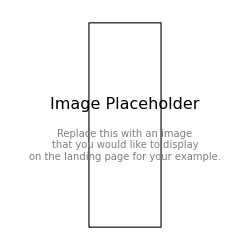

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

parameter-shift rule

Unitary operator

HErmitian operator

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.